# Determination of timing cuts

## 1. Methodology

I am going to use the Δt data of different PMT channels. The PMT’s are at both ends of the plastic scintillators (PS) and labeled connected to the WaveCatcher (WC) channels 10-13 (see the Wiki for the exact geometry).
I calculated the cfd-times of each event where all 6 PMT’s (4 from large PS, 2 from small PS) fired. The 2 small PS are orthogonal to the large PS, thus events where all PMT’s fired could only cross the detector at a small cross-section. The small PS are aligned in a such a way that a cosmic muon (coming from above) that triggers all 6 PMT’s basically simultaneously crosses the detector orthogonally.
I then calculated Δt_(13,12)=t_(trigger,13)-t_(trigger,12) where t_(trigger,x) was determined using a constant fraction method (see the used macro). Same for channels 11 and 10.
This is the data I will analyse here. I am using Mathematica here, since this uses data from different runs, which is very annoying to do with ROOT and C++.

## 2. Plotting

### The data (normal + improved algo)

```mathematica
run26ch11=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run26_11-10_cfd_times_ortho_only.txt"}],"CSV"];(*C0*)
run26ch13=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run26_13-12_cfd_times_ortho_only.txt"}],"CSV"];
run28ch11=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run28_11-10_cfd_times_ortho_only.txt"}],"CSV"];(*aC2*)
run28ch13=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run28_13-12_cfd_times_ortho_only.txt"}],"CSV"];
run29ch11=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run29_11-10_cfd_times_ortho_only.txt"}],"CSV"];(*aC1*)
run29ch13=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run29_13-12_cfd_times_ortho_only.txt"}],"CSV"];
run32ch11=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run32_11-10_cfd_times_ortho_only.txt"}],"CSV"];(*mC1*)
run32ch13=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run32_13-12_cfd_times_ortho_only.txt"}],"CSV"];
run33ch11=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run33_11-10_cfd_times_ortho_only.txt"}],"CSV"];(*mC2*)
run33ch13=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run33_13-12_cfd_times_ortho_only.txt"}],"CSV"];
run34ch11=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run34_11-10_cfd_times_ortho_only.txt"}],"CSV"];(*C1*)
run34ch13=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run34_13-12_cfd_times_ortho_only.txt"}],"CSV"];
run35ch11=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run35_11-10_cfd_times_ortho_only.txt"}],"CSV"];(*C2*)
run35ch13=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run35_13-12_cfd_times_ortho_only.txt"}],"CSV"];

run26ch11imp=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run26_11-10_improv_cfd_times_ortho_only.txt"}],"CSV"];(*C0*)
run26ch13imp=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run26_13-12_improv_cfd_times_ortho_only.txt"}],"CSV"];
run28ch11imp=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run28_11-10_improv_cfd_times_ortho_only.txt"}],"CSV"];(*aC2*)
run28ch13imp=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run28_13-12_improv_cfd_times_ortho_only.txt"}],"CSV"];
run29ch11imp=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run29_11-10_improv_cfd_times_ortho_only.txt"}],"CSV"];(*aC1*)
run29ch13imp=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run29_13-12_improv_cfd_times_ortho_only.txt"}],"CSV"];
run32ch11imp=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run32_11-10_improv_cfd_times_ortho_only.txt"}],"CSV"];(*mC1*)
run32ch13imp=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run32_13-12_improv_cfd_times_ortho_only.txt"}],"CSV"];
run33ch11imp=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run33_11-10_improv_cfd_times_ortho_only.txt"}],"CSV"];(*mC2*)
run33ch13imp=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run33_13-12_improv_cfd_times_ortho_only.txt"}],"CSV"];
run34ch11imp=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run34_11-10_improv_cfd_times_ortho_only.txt"}],"CSV"];(*C1*)
run34ch13imp=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run34_13-12_improv_cfd_times_ortho_only.txt"}],"CSV"];
run35ch11imp=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run35_11-10_improv_cfd_times_ortho_only.txt"}],"CSV"];(*C2*)
run35ch13imp=Flatten@Import[FileNameJoin[{NotebookDirectory[],"run35_13-12_improv_cfd_times_ortho_only.txt"}],"CSV"];
```

### Histograms

```mathematica
xmin=-15; xmax=15; nBins=200;
nevents26=Length@run26ch11[[2;;]];
nevents28=Length@run28ch11[[2;;]];
nevents29=Length@run29ch11[[2;;]];
nevents32=Length@run32ch11[[2;;]];
nevents33=Length@run33ch11[[2;;]];
nevents34=Length@run34ch11[[2;;]];
nevents35=Length@run35ch11[[2;;]];

nevents26imp=Length@run26ch11imp[[2;;]];
nevents28imp=Length@run28ch11imp[[2;;]];
nevents29imp=Length@run29ch11imp[[2;;]];
nevents32imp=Length@run32ch11imp[[2;;]];
nevents33imp=Length@run33ch11imp[[2;;]];
nevents34imp=Length@run34ch11imp[[2;;]];
nevents35imp=Length@run35ch11imp[[2;;]];

Legend=Function[{C0,aC1,aC2,mC1,mC2,C1,C2},Which[C0==1, {"C0 ("<>ToString@nevents26<>" events)"},aC1==1,{"14 cm -> C1 ("<>ToString@nevents29<>" events)"},aC2==1,{"14 cm -> C2 ("<>ToString@nevents28<>" events)"},mC1==1,{"7 cm -> C1 ("<>ToString@nevents32<>" events)"},mC2==1,{"7 cm -> C2 ("<>ToString@nevents33<>" events)"},C1==1,{"20.5 cm -> C1 ("<>ToString@nevents34<>" events)"},C2==1,{"19.2 cm -> C2 ("<>ToString@nevents35<>" events)"}]];
Legendimp=Function[{C0,aC1,aC2,mC1,mC2,C1,C2},Which[C0==1, {"C0 ("<>ToString@nevents26imp<>" events, improved algo)"},aC1==1,{"14 cm -> C1 ("<>ToString@nevents29imp<>" events, improved algo)"},aC2==1,{"14 cm -> C2 ("<>ToString@nevents28imp<>" events, improved algo)"},mC1==1,{"7 cm -> C1 ("<>ToString@nevents32imp<>" events, improved algo)"},mC2==1,{"7 cm -> C2 ("<>ToString@nevents33imp<>" events, improved algo)"},C1==1,{"20.5 cm -> C1 ("<>ToString@nevents34imp<>" events, improved algo)"},C2==1,{"19.2 cm -> C2 ("<>ToString@nevents35imp<>" events, improved algo)"}]];
```

### Determining timing cuts from means

```mathematica
{Mean[run34ch11imp[[2;;]]],StandardDeviation[run34ch11imp[[2;;]]]} (*C1*)
{Mean[run34ch13imp[[2;;]]],StandardDeviation[run34ch13imp[[2;;]]]}
nevents34imp
```

{2.53845,2.26166}

{3.12394,3.01162}

169

```mathematica
{Mean[run35ch11imp[[2;;]]],StandardDeviation[run35ch11imp[[2;;]]]}(*C2*)
{Mean[run35ch13imp[[2;;]]],StandardDeviation[run35ch13imp[[2;;]]]}
nevents35imp
```

{-1.51361,2.09072}

This “-1.51361” is very likely to be caused by statistics. The timing cuts implemented should be the same as for channel 13 - 12.

{-2.16723,3.08578}

157

```mathematica
{Mean[run28ch11imp[[2;;]]],StandardDeviation[run28ch11imp[[2;;]]]}(*mC2*)
{Mean[run28ch13imp[[2;;]]],StandardDeviation[run28ch13imp[[2;;]]]}
```

{-1.9272,1.97968}

{-1.72573,2.74128}

```mathematica
{Mean[run33ch11imp[[2;;]]],StandardDeviation[run33ch11imp[[2;;]]]}(*aC2*)
{Mean[run33ch13imp[[2;;]]],StandardDeviation[run33ch13imp[[2;;]]]}
```

{-0.576296,1.83981}

{-0.609401,2.37775}

```mathematica
{Mean[run26ch11imp[[2;;]]],StandardDeviation[run26ch11imp[[2;;]]]}(*C0*)
{Mean[run26ch13imp[[2;;]]],StandardDeviation[run26ch13imp[[2;;]]]}
```

{0.302976,1.67625}

{0.622108,2.25017}

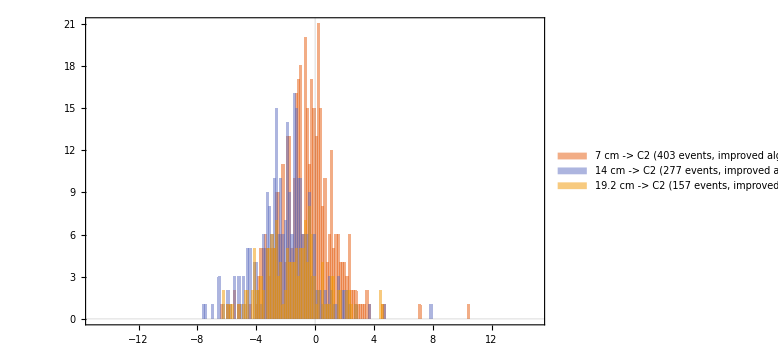

```mathematica
Histogram[{run33ch11imp[[2;;]],run28ch11imp,run35ch11imp[[2;;]]},{(Abs[xmin]+Abs[xmax])/nBins},PlotRange->{{xmin,xmax},Automatic},PlotTheme->"Scientific",ChartLegends->Join[Legendimp[0,0,0,0,1,0,0],Legendimp[0,0,1,0,0,0,0],Legendimp[0,0,0,0,0,0,1]],LabelStyle->{Black,15},ImageSize->Large]
```

### Plotting

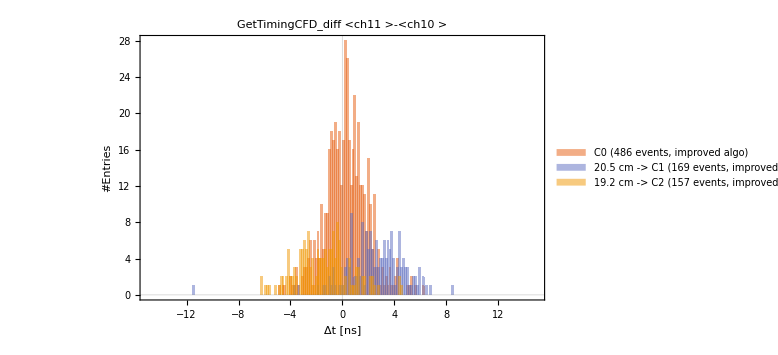

```mathematica
Histogram[{run26ch11imp[[2;;]],run34ch11imp[[2;;]],run35ch11imp[[2;;]]},{(Abs[xmin]+Abs[xmax])/nBins},PlotRange->{{xmin,xmax},Automatic},PlotTheme->"Scientific",FrameLabel->{"Δt [ns]","#Entries"},PlotLabel->"GetTimingCFD_diff <ch11 >-<ch10 >",ChartLegends->Join[Legendimp[1,0,0,0,0,0,0],Legendimp[0,0,0,0,0,1,0],Legendimp[0,0,0,0,0,0,1]],LabelStyle->{Black,15},ImageSize->Large]
```

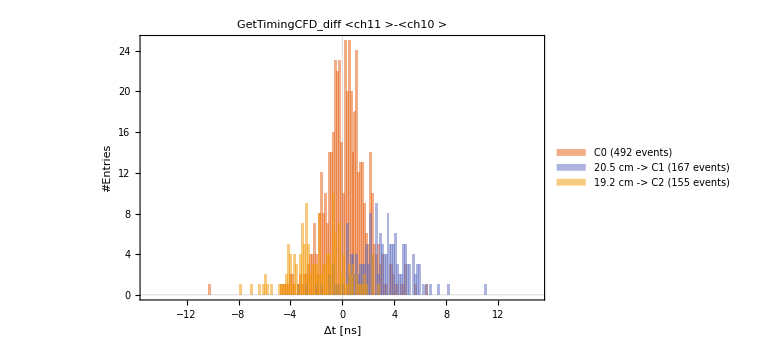

```mathematica
Histogram[{run26ch11[[2;;]],run34ch11[[2;;]],run35ch11[[2;;]]},{(Abs[xmin]+Abs[xmax])/nBins},PlotRange->{{xmin,xmax},Automatic},PlotTheme->"Scientific",FrameLabel->{"Δt [ns]","#Entries"},PlotLabel->"GetTimingCFD_diff <ch11 >-<ch10 >",ChartLegends->Join[Legend[1,0,0,0,0,0,0],Legend[0,0,0,0,0,1,0],Legend[0,0,0,0,0,0,1]],LabelStyle->{Black,15},ImageSize->Large]
```

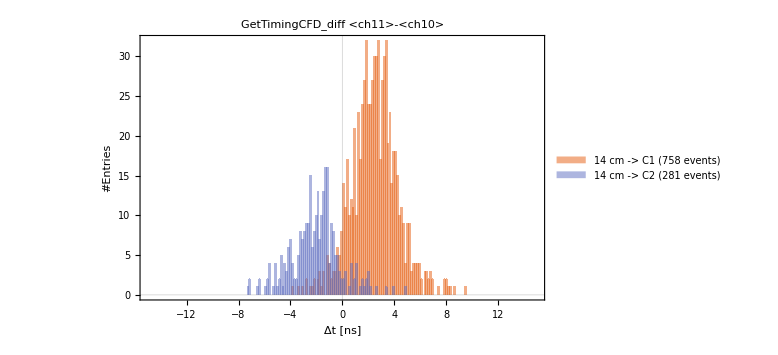

```mathematica
Histogram[{run29ch11[[2;;]],run28ch11[[2;;]]},{(Abs[xmin]+Abs[xmax])/nBins},PlotRange->{{xmin,xmax},Automatic},PlotTheme->"Scientific",FrameLabel->{"Δt [ns]","#Entries"},PlotLabel->"GetTimingCFD_diff <ch11>-<ch10>",ChartLegends->Join[Legend[0,1,0,0,0,0,0],Legend[0,0,1,0,0,0,0]],LabelStyle->{Black,15},ImageSize->Large]
```

```mathematica
Mean[run34ch13[[2;;]]]
StandardDeviation[run34ch13[[2;;]]]
Mean[run35ch13[[2;;]]]
StandardDeviation[run35ch13[[2;;]]]
```

3.47092

2.96651

-2.82684

2.64533

## 3. Timing cuts and contamination (nb: normalization)

### Cutting on the data

The following function produces a list where all events in “data” are in between “tmin” and “tmax”

```mathematica
CutFunk=Function[{data,tmin,tmax,iterations},memory={1};
For[i=2,i<iterations+2,i++,If[(data[[i]]>tmin)&&(data[[i]]<tmax),
AppendTo[memory,data[[i]]
]]];Delete[memory,1]];
```

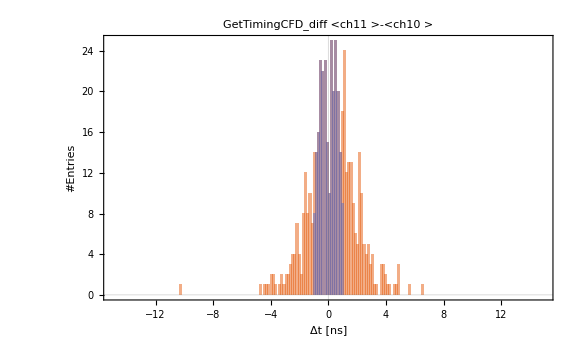

```mathematica
run26ch11cut=CutFunk[run26ch11,-1,1,nevents26];
Histogram[{run26ch11,run26ch11cut},{(Abs[xmin]+Abs[xmax])/nBins},PlotRange->{{xmin,xmax},Automatic},PlotTheme->"Scientific",FrameLabel->{"Δt [ns]","#Entries"},PlotLabel->"GetTimingCFD_diff <ch11 >-<ch10 >",LabelStyle->{Black,15},ImageSize->Large]
```